```mathematica
Clear["Global`*"]
<<MaTeX`
PathNumber=4;
CodePath[i_]=Piecewise[{{"/home/mahdawi/DAMIC/Codes/",i==1},{"/home/users2/msm550/Desktop/Dropbox/Physics/Research/H-dibaryon/XQC/Codes/",i==2},{"C:\\Users\\shafi\\Desktop\\Dropbox\\Physics\\Research\\H-dibaryon\\DAMIC\\Codes\\0\\",i==3},{"/Users/Shafi/Dropbox/Physics/Research/H-dibaryon/XQC/Codes/",i==4}}];
FigPath[i_]=Piecewise[{{"/home/mahdawi/DAMIC/Figures/",i==1},{"/home/users2/msm550/Desktop/Dropbox/Physics/Research/H-dibaryon/DAMIC/Figures/",i==2},{"C:\\Users\\shafi\\Desktop\\Dropbox\\Physics\\Research\\H-dibaryon\\DAMIC\\Figures\\",i==3},{"/Users/Shafi/Dropbox/Physics/Research/H-dibaryon/DAMIC/Figures/",i==4}}];
SetDirectory[CodePath[PathNumber]];
v0=2.20;
vE=2.30;
vesc=5.84;
norm=Integrate[v(Exp[-((v-vE)/v0)^2]-Exp[-(vesc/v0)^2]),{v,0,vE+vesc}]-Integrate[v(Exp[-((v+vE)/v0)^2]-Exp[-(vesc/v0)^2]),{v,0,vesc-vE}];
pdf[v_]=v (Exp[-((v-vE)/v0)^2]-Exp[-(vesc/v0)^2]-(Exp[-((v+vE)/v0)^2]-Exp[-(vesc/v0)^2])(1-HeavisideTheta[v-vesc+vE]))/norm;
cdf[vi_]=Integrate[pdf[v],{v,0,vi}];
inverse=Interpolation[Table[{cdf[vi],vi},{vi,0,vesc+vE,(vesc+vE)/10^5}]];
vc=3000;
```

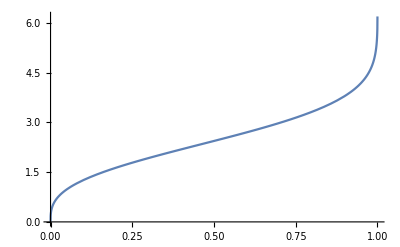

```mathematica
Plot[inverse[x],{x,0,1}]
```

```mathematica
dis=ParallelTable[{Abs[inverse[RandomVariate[UniformDistribution[]]]]/vc},{10^6}];
Export["vi_Erickeck.dat",dis];
```

```mathematica
ss=Import["vi_Erickeck.dat","Data"];
vc=3000;
vI=Table[100vc ss[[i]][[1]],{i,1,2*10^5}];
```

```mathematica
vI=Table[100vc ss[[i]][[1]],{i,1,2*10^5}];
vIhistogram=Histogram[{vI},45,"PDF",ChartStyle->{{Gray},Directive[EdgeForm[]]},Frame->True,ChartLayout->"Overlapped",FrameLabel->{{MaTeX["f(v_i)"],""},{MaTeX["v_i\\;(km/s)"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->10},AxesOrigin-> {0,0},ChartLegends->Placed[SwatchLegend[{MaTeX["Generated"]},LabelStyle->{GrayLevel[0.1],FontFamily-> "CMU Serif",10}],{0.8,0.7}]];
vMax=FindRoot[D[pdf[x],x],{x,3}][[1,2]];
lineMax=Line[{{100vMax,0},{100vMax,pdf[vMax]/100}}];
vMean=Mean[vI];
lineMean=Line[{{vMean,0},{vMean,pdf[vMean/100]/100}}];
line=ListPlot[{Table[{100v,pdf[v]/100},{v,0,vesc+vE,1/100}]},Joined->True,PlotStyle->(Directive[#,AbsoluteThickness[3]]&/@{Green}),PerformanceGoal->"Speed",Frame->True,FrameLabel->{{MaTeX["f(v_i)"],""},{MaTeX["v_i\\;(km/s)"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->10},AxesOrigin-> {0,0},PlotLegends->Placed[SwatchLegend[{MaTeX["Actual"]},LabelStyle->{GrayLevel[0.1],FontFamily-> "CMU Serif",10}],{0.8,0.7}],Epilog->{Directive[Red,Dashed,AbsoluteThickness[2]],lineMax},Prolog->{Directive[Purple,DotDashed,AbsoluteThickness[1.5]],lineMean}];
p=Show[line,vIhistogram]
Export[FigPath[PathNumber]<>"Maxwellian.pdf",p,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

-Graphics-

/Users/Shafi/Dropbox/Physics/Research/H-dibaryon/DAMIC/Figures/Maxwellian.pdf

```mathematica
vMean
```

346.63

```mathematica
vMax
```

3.2626

```mathematica
Clear["Global`*"]
<<MaTeX`
PathNumber=4;
CodePath[i_]=Piecewise[{{"/home/mahdawi/DAMIC/Codes/",i==1},{"/home/users2/msm550/Desktop/Dropbox/Physics/Research/H-dibaryon/XQC/Codes/",i==2},{"/Users/s/Google Drive/Physics/Research/H-dibaryon/XQC/Codes/",i==3},{"/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/XQC/Codes/",i==4}}];
FigPath[i_]=Piecewise[{{"/home/mahdawi/DAMIC/Figures/",i==1},{"/home/users2/msm550/Desktop/Dropbox/Physics/Research/H-dibaryon/DAMIC/Figures/",i==2},{"/Users/s/Google Drive/Physics/Research/H-dibaryon/DAMIC/Latex/Figures/",i==3},{"/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Latex/Figures/",i==4}}];
SetDirectory[CodePath[PathNumber]];
v0=220;
vesc=584;
norm=Integrate[v^2Exp[-(v/v0)^2],{v,0,vesc}];
pdf[v_]=v^2Exp[-(v/v0)^2]/norm;
cdf[vi_]=Integrate[pdf[v],{v,0,vi}];
inverse=Interpolation[Table[{N[cdf[vi],665],vi},{vi,0,vesc}]];
vc=300000;
```

```mathematica
vDMHalo=ParallelTable[{ Abs[inverse[RandomVariate[UniformDistribution[]]]]/vc,RandomVariate[UniformDistribution[{-1,1}]]},{10^6}];
Export["vi_g_30.dat",vDMHalo];
```

$Aborted

```mathematica
vDetHalo={39.14,230.5,3.57};
vDMHalo=ParallelTable[Abs[inverse[RandomVariate[UniformDistribution[]]]],{10^6}];
angles=ParallelTable[{RandomVariate[UniformDistribution[{-1,1}]],RandomVariate[UniformDistribution[{0,2 Pi}]]},{10^6}];
vDMHalo3=ParallelTable[{vDMHalo[[i]]Sin[ArcCos[angles[[i,1]]]]Cos[angles[[i,2]]],vDMHalo[[i]]Sin[ArcCos[angles[[i,1]]]]Sin[angles[[i,2]]],vDMHalo[[i]]angles[[i,1]]},{i,10^6}];
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["/Applications/Mathematica.app/Contents/MacOS/WolframKernel" -subkernel -noinit -wstp,1402,5].

LinkObject::linkd: Unable to communicate with closed link LinkObject["/Applications/Mathematica.app/Contents/MacOS/WolframKernel" -subkernel -noinit -wstp,1403,6].

Parallel`Developer`ConnectKernel::failinit: 2 of 2 kernels failed to initialize.

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

$Aborted

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

$Aborted

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

Part::partd: Part specification vDMHalo⟦1⟧ is longer than depth of object.

Part::partd: Part specification angles⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification angles⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Aborted

```mathematica
vDMDetEarth=ParallelTable[{vDMHalo3[[i,1]]-vDetHalo[[1]],vDMHalo3[[i,2]]-vDetHalo[[2]],vDMHalo3[[i,3]]-vDetHalo[[3]]}/vc,{i,10^6}];
rot[l_,b_]:={Cos[l Pi/180]Cos[b Pi/180],Sin[l Pi/180]Cos[b Pi/180],Sin[b Pi/180]}
RDet=rot[90,60];
RLaunch1=rot[71,54];
RLaunch2=rot[75,82];
vNorm=ParallelTable[Norm[vDMDetEarth[[i]]],{i,10^6}];
vDMDetS=ParallelTable[{vNorm[[i]],angles[[i,1]],vDMDetEarth[[i,2]]/vNorm[[i]],RLaunch1.vDMDetEarth[[i]]/vNorm[[i]],RDet.vDMDetEarth[[i]]/vNorm[[i]],RLaunch2.vDMDetEarth[[i]]/vNorm[[i]]},{i,10^6}];
```

```mathematica
vDMDetS=Sort[vDMDetS,#1[[5]]<#2[[5]]&];
Export["viE_sortedDet.dat",vDMDetS];
```

```mathematica
a={{1,2,6},{3,4,5},{8,3,5}};
Sort[a,#1[[3]]>#2[[3]]&]
```

{{1,2,6},{8,3,5},{3,4,5}}

```mathematica
vDMDetS=Sort[vDMDetS,#1[[4]]<#2[[4]]&];
Export["viE_sortedLaunch.dat",vDMDetS];
```

```mathematica
vDMDetS=Sort[vDMDetS,#1[[1]]>#2[[1]]&];
Export["viE_sortedNorm.dat",vDMDetS];
```

```mathematica
vDMDetS=Sort[vDMDetS,#1[[6]]<#2[[6]]&];
Export["viEb82_sortedLaunch.dat",vDMDetS];
```

```mathematica
Euler[α,β,γ].{x,y,z}//MatrixForm
```

(z Sin[α] Sin[β]+y (-Cos[β] Cos[γ] Sin[α]-Cos[α] Sin[γ])+x (Cos[α] Cos[γ]-Cos[β] Sin[α] Sin[γ])
-z Cos[α] Sin[β]+x (Cos[γ] Sin[α]+Cos[α] Cos[β] Sin[γ])+y (Cos[α] Cos[β] Cos[γ]-Sin[α] Sin[γ])
z Cos[β]+y Cos[γ] Sin[β]+x Sin[β] Sin[γ])

```mathematica
myArcTan[x_,y_]:=Piecewise[{{ArcTan[x,y],y>0 },{2Pi+ArcTan[x,y],y<0 }}]
vDMDetS=ParallelTable[{Norm[vDMDet[[i]]],vDMDet[[i,3]]/Norm[vDMDet[[i]]],myArcTan[vDMDet[[i,1]],vDMDet[[i,2]]]},{i,10^6}];
```

```mathematica
RDet
```

{{1,0,0},{0,1/2,-(√3)/2},{0,(√3)/2,1/2}}

```mathematica
Euler[Pi(-90-90)/180,Pi 60/180,0].{0,1,0}
```

{0,-1/2,(√3)/2}

```mathematica
RotationMatrix[{{0,1,0},{1/4,Sqrt[3]/4,Sqrt[3]/2}}].{0,1,0}
```

{1/4,(√3)/4,(√3)/2}

```mathematica
RotationMatrix[{{0,1,0},{0,1/2,Sqrt[3]/2}}].{0,1,0}
```

{0,1/2,(√3)/2}

```mathematica
rot1[l_,b_]:=RotationMatrix[{{0,1,0},{Sin[(90-b)  Pi/180]Cos[l Pi/180],Sin[(90-b)  Pi/180]Sin[l Pi/180],Cos[(90-b) Pi/180]}}]
rot1[90,60]
```

{{1,0,0},{0,1/2,-(√3)/2},{0,(√3)/2,1/2}}

```mathematica
Euler[α_,β_,γ_]:={{Cos[α]  Cos[γ]-Cos[β]Sin[α] Sin[γ],-Sin[γ] Cos[α]-Sin[α] Cos[β] Cos[γ],Sin[α] Sin[β]},{ Cos[γ] Sin[α]+Cos[β]Cos[α] Sin[γ],Cos[α] Cos[γ]Cos[β]- Sin[α] Sin[γ],-Cos[α] Sin[β]},{Sin[γ] Sin[β],Sin[β] Cos[γ],Cos[β]}}
rot[l_,b_]:=Euler[Pi(l-90)/180,Pi b/180,0]
rot1[90,60]
```

{{1,0,0},{0,1/2,-(√3)/2},{0,(√3)/2,1/2}}

```mathematica
rot1[l_,b_]:={Sin[b Pi/180]Cos[l Pi/180],Sin[b Pi/180]Sin[l Pi/180],Cos[b Pi/180]}
rot1[90,60]
```

{0,(√3)/2,1/2}

```mathematica
vDMDetS=Import["viE_sortedDet.dat","Data"];
```

```mathematica
vDMDetS[[1.09 10^5,5]]
```

-0.849117

```mathematica
gframe=HistogramList[Table[vDMDetS[[i,2]],{i,10^6}],{Table[.05(i-1),{i,-19,21}]},"PDF"];
lframe=HistogramList[Table[vDMDetS[[i,4]],{i,10^6}],{Table[.05(i-1),{i,-19,21}]},"PDF"];
lframeb82=HistogramList[Table[vDMDetS[[i,6]],{i,10^6}],{Table[.05(i-1),{i,-19,21}]},"PDF"];
dframe=HistogramList[Table[vDMDetS[[i,5]],{i,10^6}],{Table[.05(i-1),{i,-19,21}]},"PDF"];
```

```mathematica
cosdis=ListLinePlot[{Transpose[{gframe[[1]],Join[gframe[[2]],{gframe[[2,-1]]}]}],Transpose[{lframe[[1]],Join[lframe[[2]],{lframe[[2,-1]]}]}],Transpose[{dframe[[1]],Join[dframe[[2]],{dframe[[2,-1]]}]}]},PlotStyle->{{Opacity[0.7],Gray},{Opacity[0.7],Darker[Cyan]},{Opacity[0.7],Orange}},InterpolationOrder->0,Filling->Axis,FillingStyle->{{Opacity[0.2],Darker[Cyan]},{Opacity[0.2],Purple},{Opacity[0.2],Orange}},Frame->True,FrameLabel->{{MaTeX["Probability\\;distribution"],""},{MaTeX["cos\\,\\theta"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->13},PlotLegends->Placed[SwatchLegend[{MaTeX["Galactic\\;frame"],MaTeX["XQC\\;launch"],MaTeX["XQC\\;detection"]},LabelStyle->{GrayLevel[0.1],FontFamily-> "CMU Serif",10}],{0.825,0.75}],Axes->{True,False}];
ES=ContourPlot[x==0.25,{x,-2,2},{y,0,1.05},ContourStyle->{Purple,Dashed}];
BS=ContourPlot[x==-0.848,{x,-2,2},{y,0,1.05},ContourStyle->{Red,DotDashed}];
Graphics[Text[Rotate[MaTeX["60\,eV"],Pi/2],{Log[60-2],0.9935},Background-> White]];
EStxt=Graphics[Text[Rotate[MaTeX["ES\\;threshold"],Pi/2],{0.17,0.25},Background-> White]];
BStxt=Graphics[Text[Rotate[MaTeX["BS\\;threshold"],Pi/2],{-0.75,0.25},Background-> White]];
p1=Show[cosdis,ES,EStxt,BS,BStxt]
Export[FigPath[PathNumber]<>"Zenith_angle_dis.pdf",p1,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

-Graphics-

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Latex/Figures/Zenith_angle_dis.pdf

```mathematica
cosdis=ListLinePlot[{Transpose[{gframe[[1]],Join[gframe[[2]],{gframe[[2,-1]]}]}],Transpose[{lframe[[1]],Join[lframe[[2]],{lframe[[2,-1]]}]}],Transpose[{lframeb82[[1]],Join[lframeb82[[2]],{lframeb82[[2,-1]]}]}],Transpose[{dframe[[1]],Join[dframe[[2]],{dframe[[2,-1]]}]}]},PlotStyle->{{Opacity[0.7],Gray},{Opacity[0.7],Darker[Cyan]},{Opacity[0.7],Purple},{Opacity[0.7],Orange}},InterpolationOrder->0,Filling->Axis,FillingStyle->{{Opacity[0.2],Gray},{Opacity[0.2],Darker[Cyan]},{Opacity[0.2],Purple},{Opacity[0.2],Orange}},Frame->True,FrameLabel->{{MaTeX["Probability\\;distribution"],""},{MaTeX["cos\\,\\theta"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->13},PlotLegends->SwatchLegend[{MaTeX["Galactic\\;frame"],MaTeX["XQC\\;launch\\;(b=54)"],MaTeX["XQC\\;launch\\;(b=82)"],MaTeX["XQC\\;detection"]},LabelStyle->{GrayLevel[0.1],FontFamily-> "CMU Serif",10}],Axes->{True,False}];
ES=ContourPlot[x==0.25,{x,-2,2},{y,0,1.05},ContourStyle->{Purple,Dashed}];
BS=ContourPlot[x==-0.848,{x,-2,2},{y,0,1.05},ContourStyle->{Red,DotDashed}];
Graphics[Text[Rotate[MaTeX["60\,eV"],Pi/2],{Log[60-2],0.9935},Background-> White]];
EStxt=Graphics[Text[Rotate[MaTeX["ES\\;threshold"],Pi/2],{0.17,0.25},Background-> White]];
BStxt=Graphics[Text[Rotate[MaTeX["BS\\;threshold"],Pi/2],{-0.75,0.25},Background-> White]];
p1=Show[cosdis,ES,EStxt,BS,BStxt]
Export[FigPath[PathNumber]<>"Zenith_angle_dis(v2).pdf",p1,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

-Graphics-

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Latex/Figures/Zenith_angle_dis(v2).pdf

```mathematica
v=Import["viE_sortedLaunch.dat","Data"];
vb82=Import["viEb82_sortedLaunch.dat","Data"];
```

```mathematica
all=HistogramList[Table[300000v[[i,1]],{i,10^6}],{Table[20(i-1),{i,43}]},"PDF"];
b54=HistogramList[Table[300000v[[i,1]],{i,9.0256*10^5}],{Table[20(i-1),{i,43}]},"PDF"];
b82=HistogramList[Table[300000vb82[[i,1]],{i,7.565*10^5}],{Table[20(i-1),{i,43}]},"PDF"];
```

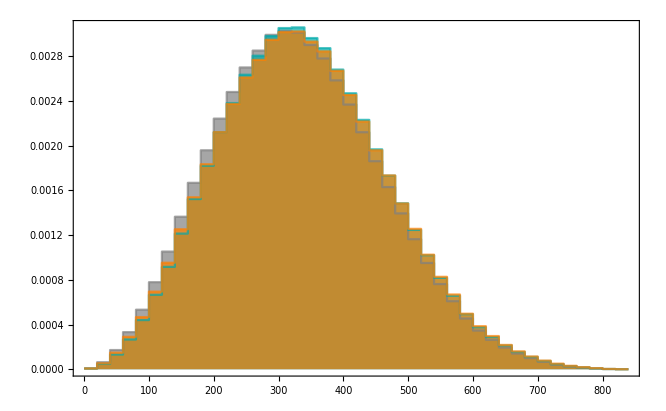

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Latex/Figures/speed_dis(v2).pdf

```mathematica
vdis=ListLinePlot[{Transpose[{all[[1]],Join[all[[2]],{all[[2,-1]]}]}],Transpose[{b54[[1]],Join[b54[[2]],{b54[[2,-1]]}]}],Transpose[{b82[[1]],Join[b82[[2]],{b82[[2,-1]]}]}]},PlotStyle->{{Opacity[0.7],Gray},{Opacity[0.7],Darker[Cyan]},{Opacity[0.7],Orange}},InterpolationOrder->0,Filling->Axis,FillingStyle->{{Opacity[0.2],Gray},{Opacity[0.2],Darker[Cyan]},{Opacity[0.2],Orange}},Frame->True,FrameLabel->{{MaTeX["Probability\\;distribution"],""},{MaTeX["v\\;(\\,km/s\\,)"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->13},PlotLegends->Placed[SwatchLegend[{MaTeX["all\\;particles"],MaTeX["not\\;shielded\\,(b=54)"],MaTeX["not\\;shielded\\,(b=82)"]},LabelStyle->{GrayLevel[0.1],FontFamily-> "CMU Serif",10}],{0.77,0.75}],Axes->{True,False}]
Export[FigPath[PathNumber]<>"speed_dis(v2).pdf",vdis,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

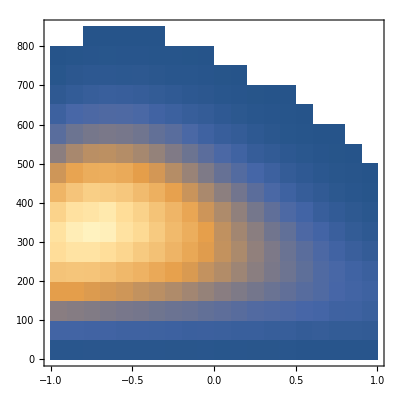
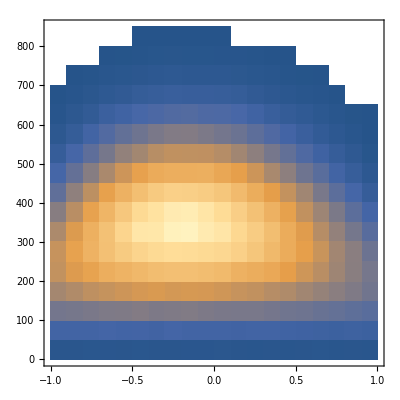

```mathematica
{DensityHistogram[Table[{v[[i,4]],vc v[[i,1]]},{i,10^6}],Frame->True,FrameLabel->{{MaTeX["v\\,(km/s)"],""},{MaTeX["cos(\\theta)"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->10},AxesOrigin-> {0,0}],DensityHistogram[Table[{vb82[[i,4]],vc vb82[[i,1]]},{i,10^6}],Frame->True,FrameLabel->{{MaTeX["v\\,(km/s)"],""},{MaTeX["cos(\\theta)"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->10},AxesOrigin-> {0,0}]}
```

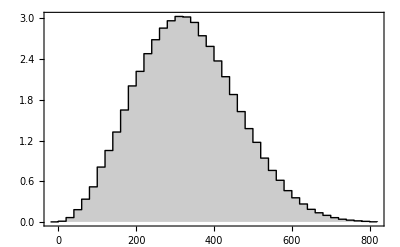

/Users/Shafi/Dropbox/Physics/Research/H-dibaryon/DAMIC/Figures/Maxwellian_Erickeck.pdf

```mathematica
vDMDet=Import["vi_Erickeck_3.dat","Data"];
vI2=Table[300000 vDMDet[[i]][[1]],{i,1,2*10^5}];
<<MaTeX`
hd=HistogramList[vI2,45];
histPlotAdjust[histList_]:=Module[{bins,counts},With[{binLength=histList[[1,2]]-First@histList[[1]]},bins={First@histList[[1]]-binLength}~Join~histList[[1]];
counts={0}~Join~(1000histList[[2]]/Length[vI2]/binLength)~Join~{0};
{bins,counts}]]
hd=histPlotAdjust[hd];
vIhistogram=ListLinePlot[Transpose[hd],InterpolationOrder->0,PlotStyle->Directive[Thick,Black],PlotStyle->Thick,Filling->Axis,Frame->True,FrameLabel->{{MaTeX["f(v)\\times10^3"],""},{MaTeX["v\\;(km/s)"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->10},AxesOrigin-> {0,0}]
Export[FigPath[PathNumber]<>"Maxwellian_Erickeck.pdf",vIhistogram,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

```mathematica
vDMg=Import["vi_g.dat","Data"];
vI2=Table[300000 vDMg[[i]][[1]],{i,1,2*10^5}];
<<MaTeX`
hd=HistogramList[vI2,45];
histPlotAdjust[histList_]:=Module[{bins,counts},With[{binLength=histList[[1,2]]-First@histList[[1]]},bins={First@histList[[1]]-binLength}~Join~histList[[1]];
counts={0}~Join~(1000histList[[2]]/Length[vI2]/binLength)~Join~{0};
{bins,counts}]]
hd=histPlotAdjust[hd];
vIhistogram2=ListLinePlot[Transpose[hd],InterpolationOrder->0,PlotStyle->Directive[Thick,Orange],PlotStyle->Thick,Filling->Axis,Frame->True,FrameLabel->{{MaTeX["f(v)\\times10^3"],""},{MaTeX["v\\;(km/s)"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->10},AxesOrigin-> {0,0},PlotRange->{{0,850},{0,4}}];
vDMg=Import["vi_g_30.dat","Data"];
vI2=Table[300000 vDMg[[i]][[1]],{i,1,2*10^5}];
<<MaTeX`
hd=HistogramList[vI2,45];
histPlotAdjust[histList_]:=Module[{bins,counts},With[{binLength=histList[[1,2]]-First@histList[[1]]},bins={First@histList[[1]]-binLength}~Join~histList[[1]];
counts={0}~Join~(1000histList[[2]]/Length[vI2]/binLength)~Join~{0};
{bins,counts}]]
hd=histPlotAdjust[hd];
vIhistogram3=ListLinePlot[Transpose[hd],InterpolationOrder->0,PlotStyle->Directive[Thick,Blue],PlotStyle->Thick,Filling->Axis,Frame->True,FrameLabel->{{MaTeX["f(v)\\times10^3"],""},{MaTeX["v\\;(km/s)"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->10},AxesOrigin-> {0,0},PlotRange->{{0,850},{0,28}}];
```

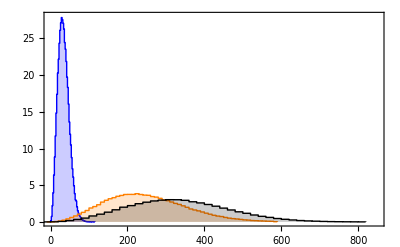

/Users/Shafi/Dropbox/Physics/Research/H-dibaryon/DAMIC/Figures/Maxwellian_Extreme.pdf

```mathematica
vEx=Show[vIhistogram3,vIhistogram2,vIhistogram]
Export[FigPath[PathNumber]<>"Maxwellian_Extreme.pdf",vEx,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

```mathematica
v=Import["viE_sortedLaunch.dat","Data"][[All,1]];
v650=Import["viE650_sortedLaunch.dat","Data"][[All,1]];
```

```mathematica
vh=HistogramList[Table[300000v[[i]],{i,10^6}],{Table[20(i-1),{i,45}]},"PDF"];
v650h=HistogramList[Table[300000v650[[i]],{i,10^6}],{Table[20(i-1),{i,45}]},"PDF"];
```

```mathematica
vh[[2]]
v650h[[2]]
```

{91/10000000,1293/20000000,1683/10000000,67/200000,5349/10000000,1569/2000000,21051/20000000,26817/20000000,33163/20000000,19707/10000000,44731/20000000,12557/5000000,2173/800000,57167/20000000,59591/20000000,12011/4000000,59711/20000000,14553/5000000,5551/2000000,52097/20000000,2963/1250000,21131/10000000,9407/5000000,32547/20000000,13723/10000000,4611/4000000,18891/20000000,15373/20000000,11959/20000000,2307/5000000,1423/4000000,2691/10000000,3851/20000000,551/4000000,1913/20000000,1319/20000000,217/5000000,101/4000000,319/20000000,147/20000000,7/5000000,0,0,0}

{87/10000000,643/10000000,3463/20000000,653/2000000,527/1000000,1547/2000000,21271/20000000,13313/10000000,33177/20000000,39141/20000000,44867/20000000,49859/20000000,26861/10000000,14319/5000000,29763/10000000,12077/4000000,59843/20000000,57967/20000000,55493/20000000,2587/1000000,47301/20000000,42317/20000000,4739/2500000,16181/10000000,27457/20000000,37/32000,19001/20000000,3091/4000000,6027/10000000,581/1250000,7179/20000000,2707/10000000,1917/10000000,2831/20000000,2003/20000000,29/400000,251/5000000,169/5000000,213/10000000,251/20000000,77/10000000,41/10000000,13/5000000,1/2500000}

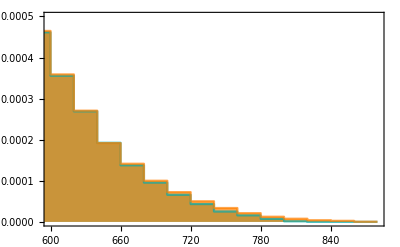

```mathematica
vdis=ListLinePlot[{Transpose[{vh[[1]],Join[vh[[2]],{vh[[2,-1]]}]}],Transpose[{v650h[[1]],Join[v650h[[2]],{v650h[[2,-1]]}]}]},PlotStyle->{{Opacity[0.7],Darker[Cyan]},{Opacity[0.7],Orange}},InterpolationOrder->0,Filling->Axis,FillingStyle->{{Opacity[0.2],Darker[Cyan]},{Opacity[0.2],Orange}},Frame->True,FrameLabel->{{MaTeX["Probability\\;distribution"],""},{MaTeX["v\\;(\\,km/s\\,)"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->13},PlotLegends->Placed[SwatchLegend[{MaTeX["584\\,km/s"],MaTeX["650\\,km/s"]},LabelStyle->{GrayLevel[0.1],FontFamily-> "CMU Serif",10}],{0.825,0.75}],Axes->{True,False},PlotRange->{{600,880},{-.0000,0.0005}}]
```

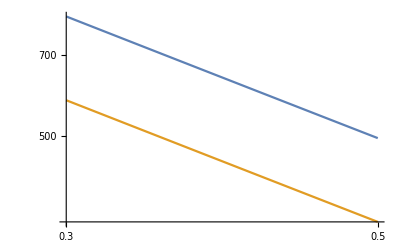

```mathematica
mu[m1_,m2_]:=m1 m2/(m1+m2)
A=28;
mp=.938;
vm[m_]:=300000Sqrt[A mp 2.5 10^-8]/mu[m,A mp] 
LogLogPlot[{vm[m],vm[m]/Sqrt[2]},{m,0.3,0.5},PlotRange->All]
```

```mathematica
norm=NIntegrate[v f[v],{v,0,816/300000}];
cdfv[vi_]:=NIntegrate[v f[v],{v,0,vi}]/norm;
inverse=Interpolation[Table[{cdfv[vi],vi},{vi,0,816/300000,10^-5}]];
dis=ParallelTable[{Abs[inverse[RandomVariate[UniformDistribution[]]]]},{10^6}];
```

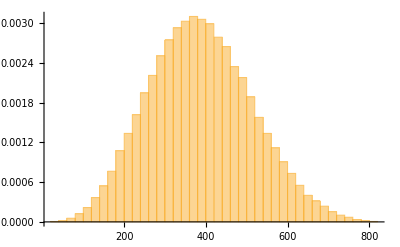

```mathematica
vI=Table[vc dis[[i]][[1]],{i,1,2*10^5}];
vIhistogram=Histogram[{vI},45,"PDF"]
```

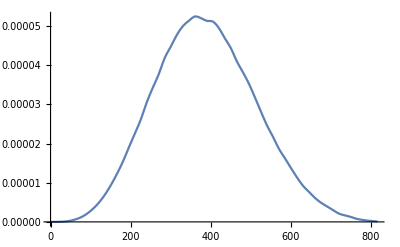

```mathematica
line=ListPlot[{Table[{vc v, v f[v]},{v,0,816/300000,10^-5}]},Joined->True]
```

```mathematica
norm=Integrate[v^2(Exp[-((v-vE)/v0)^2]-Exp[-(vesc/v0)^2]),{v,0,vE+vesc}]-Integrate[v^2(Exp[-((v+vE)/v0)^2]-Exp[-(vesc/v0)^2]),{v,0,vesc-vE}];
pdf[v_]=v ^2(Exp[-((v-vE)/v0)^2]-Exp[-(vesc/v0)^2]-(Exp[-((v+vE)/v0)^2]-Exp[-(vesc/v0)^2])(1-HeavisideTheta[v-vesc+vE]))/norm;
cdf[vi_]=Integrate[pdf[v],{v,0,vi}];
inverse=Interpolation[Table[{cdf[vi],vi},{vi,0,vesc+vE,(vesc+vE)/10^5}]];
vc=3000;
```

Interpolation::inddp: The point 1.32718×10^-16 in dimension 1 is duplicated.

```mathematica
dis=ParallelTable[{Abs[inverse[RandomVariate[UniformDistribution[]]]]},{10^6}];
```

Interpolation::inddp: The point 1.32718×10^-16 in dimension 1 is duplicated.

```mathematica
vI2=Table[100vc dis[[i]][[1]],{i,1,2*10^5}];
vIhistogram2=Histogram[{vI2},45,"PDF"]
```